# Generate Quantum Expressions for Papers, Books and Other Publications

by José Luis Gómez-Muñoz
http://homepage.cem.itesm.mx/lgomez/quantum/
jose.luis.gomez@itesm.mx

## Introduction

This is a tutorial on the use of Quantum`Computing` Mathematica add-on to generate Quantum expressions that can be copy-pasted to other editors.

## Load the Package

First load the Quantum`Computing` package. Write:
Needs["Quantum`Computing`"];
then press at the same time the keys ⇧-⌤ to evaluate. Mathematica will load the package. The semicolon prevents Mathematica from printing the welcome message:

```mathematica
Needs["Quantum`Computing`"]
```

In order to use the keyboard to enter quantum objects write:
SetComputingAliases[ ];
then press at the same time the keys ⇧-⌤ to evaluate. The semicolon prevents Mathematica from printing the help message. Remember that SetComputingAliases[ ] must be evaluated again in each new notebook:

```mathematica
SetComputingAliases[];
```

## Copy-Paste or Export to TEX editors

This is an expression in Dirac notation, with the conventions of this Mathematica add-on

```mathematica
QuantumEvaluate[Subscript[ℋ, OverHat[1]]⊗Subscript[ℋ, OverHat[2]]]
```

1/2 |0_OverHat[1],0_OverHat[2]⟩·⟨0_OverHat[1],0_OverHat[2]|+1/2 |0_OverHat[1],1_OverHat[2]⟩·⟨0_OverHat[1],0_OverHat[2]|+1/2 |1_OverHat[1],0_OverHat[2]⟩·⟨0_OverHat[1],0_OverHat[2]|+1/2 |1_OverHat[1],1_OverHat[2]⟩·⟨0_OverHat[1],0_OverHat[2]|+1/2 |0_OverHat[1],0_OverHat[2]⟩·⟨0_OverHat[1],1_OverHat[2]|-1/2 |0_OverHat[1],1_OverHat[2]⟩·⟨0_OverHat[1],1_OverHat[2]|+1/2 |1_OverHat[1],0_OverHat[2]⟩·⟨0_OverHat[1],1_OverHat[2]|-1/2 |1_OverHat[1],1_OverHat[2]⟩·⟨0_OverHat[1],1_OverHat[2]|+1/2 |0_OverHat[1],0_OverHat[2]⟩·⟨1_OverHat[1],0_OverHat[2]|+1/2 |0_OverHat[1],1_OverHat[2]⟩·⟨1_OverHat[1],0_OverHat[2]|-1/2 |1_OverHat[1],0_OverHat[2]⟩·⟨1_OverHat[1],0_OverHat[2]|-1/2 |1_OverHat[1],1_OverHat[2]⟩·⟨1_OverHat[1],0_OverHat[2]|+1/2 |0_OverHat[1],0_OverHat[2]⟩·⟨1_OverHat[1],1_OverHat[2]|-1/2 |0_OverHat[1],1_OverHat[2]⟩·⟨1_OverHat[1],1_OverHat[2]|-1/2 |1_OverHat[1],0_OverHat[2]⟩·⟨1_OverHat[1],1_OverHat[2]|+1/2 |1_OverHat[1],1_OverHat[2]⟩·⟨1_OverHat[1],1_OverHat[2]|

TraditionalForm gives an expression closer to the Dirac notation as used in books and papers

```mathematica
TraditionalForm[QuantumEvaluate[Subscript[ℋ, OverHat[1]]⊗Subscript[ℋ, OverHat[2]]]]
```

1/2 |00⟩⟨00|+1/2 |01⟩⟨00|+1/2 |10⟩⟨00|+1/2 |11⟩⟨00|+1/2 |00⟩⟨01|-1/2 |01⟩⟨01|+1/2 |10⟩⟨01|-1/2 |11⟩⟨01|+1/2 |00⟩⟨10|+1/2 |01⟩⟨10|-1/2 |10⟩⟨10|-1/2 |11⟩⟨10|+1/2 |00⟩⟨11|-1/2 |01⟩⟨11|-1/2 |10⟩⟨11|+1/2 |11⟩⟨11|

TeXForm can be used to generate an expression that can be copy-pasted to a TEX editor:

```mathematica
TeXForm[TraditionalForm[QuantumEvaluate[Subscript[ℋ, OverHat[1]]⊗Subscript[ℋ, OverHat[2]]]]]
```

\frac{1}{2} |00\rangle \langle 00|+\frac{1}{2}
   |01\rangle \langle 00|+\frac{1}{2} |10\rangle \langle
   00|+\frac{1}{2} |11\rangle \langle 00|+\frac{1}{2}
   |00\rangle \langle 01|-\frac{1}{2} |01\rangle \langle
   01|+\frac{1}{2} |10\rangle \langle 01|-\frac{1}{2}
   |11\rangle \langle 01|+\frac{1}{2} |00\rangle \langle
   10|+\frac{1}{2} |01\rangle \langle 10|-\frac{1}{2}
   |10\rangle \langle 10|-\frac{1}{2} |11\rangle \langle
   10|+\frac{1}{2} |00\rangle \langle 11|-\frac{1}{2}
   |01\rangle \langle 11|-\frac{1}{2} |10\rangle \langle
   11|+\frac{1}{2} |11\rangle \langle 11|

The standard Mathematica command Export can be used to generate a file in TEX format:

```mathematica
Export["mytest.tex",TraditionalForm[QuantumEvaluate[Subscript[ℋ, OverHat[1]]⊗Subscript[ℋ, OverHat[2]]]]]
```

mytest.tex

This is the content of the file that was created above:

```mathematica
ReadList["mytest.tex",String]
```

{%% AMS-LaTeX Created by Wolfram Mathematica 7.0 : www.wolfram.com,\documentclass{article},\usepackage{amsmath, amssymb, graphics},\newcommand{\mathsym}[1]{{}},\newcommand{\unicode}[1]{{}},\begin{document},\[\frac{1}{2} |00\rangle \langle 00|+\frac{1}{2} |01\rangle \langle 00|+\frac{1}{2} |10\rangle \langle 00|+\frac{1}{2} |11\rangle \langle 00|+\frac{1}{2},|00\rangle \langle 01|-\frac{1}{2} |01\rangle \langle 01|+\frac{1}{2} |10\rangle \langle 01|-\frac{1}{2} |11\rangle \langle 01|+\frac{1}{2} |00\rangle,\langle 10|+\frac{1}{2} |01\rangle \langle 10|-\frac{1}{2} |10\rangle \langle 10|-\frac{1}{2} |11\rangle \langle 10|+\frac{1}{2} |00\rangle \langle,11|-\frac{1}{2} |01\rangle \langle 11|-\frac{1}{2} |10\rangle \langle 11|+\frac{1}{2} |11\rangle \langle 11|\],\end{document}}

## Copy-paste Dirac Expressions as Images to Microsoft Word and Other Processors

Here we generate the Truth-Table for an operator. The resulta has the notation of this Mathematica package, which is not the same as the usual notation for Quantum Computing papers. Furthermore, this table cannot be sucessfully copy-pasted (some elements and formating is lost) to a Microsoft Word document yet, please continue reading, below in this document it will be shown how to generate expressions that can be copy-pasted (as images) to Microsoft Word.

```mathematica
QuantumTableForm[Subscript[ℋ, OverHat[1]]⊗Subscript[ℋ, OverHat[2]]]
```

|   Input |   Output
0 | |0_OverHat[1],0_OverHat[2]⟩ | 1/2 |0_OverHat[1],0_OverHat[2]⟩+1/2 |0_OverHat[1],1_OverHat[2]⟩+1/2 |1_OverHat[1],0_OverHat[2]⟩+1/2 |1_OverHat[1],1_OverHat[2]⟩
1 | |0_OverHat[1],1_OverHat[2]⟩ | 1/2 |0_OverHat[1],0_OverHat[2]⟩-1/2 |0_OverHat[1],1_OverHat[2]⟩+1/2 |1_OverHat[1],0_OverHat[2]⟩-1/2 |1_OverHat[1],1_OverHat[2]⟩
2 | |1_OverHat[1],0_OverHat[2]⟩ | 1/2 |0_OverHat[1],0_OverHat[2]⟩+1/2 |0_OverHat[1],1_OverHat[2]⟩-1/2 |1_OverHat[1],0_OverHat[2]⟩-1/2 |1_OverHat[1],1_OverHat[2]⟩
3 | |1_OverHat[1],1_OverHat[2]⟩ | 1/2 |0_OverHat[1],0_OverHat[2]⟩-1/2 |0_OverHat[1],1_OverHat[2]⟩-1/2 |1_OverHat[1],0_OverHat[2]⟩+1/2 |1_OverHat[1],1_OverHat[2]⟩

Next expression is better; TraditionalForm[] generates an expression in the notation that is usually used in papers and books. However, this table cannot be sucessfully copy-pasted (some elements and formating is lost) to a Microsoft Word document yet, please continue reading, below in this document it will be shown how to generate expressions that can be copy-pasted to Microsoft Word.

```mathematica
TraditionalForm[QuantumTableForm[Subscript[ℋ, OverHat[1]]⊗Subscript[ℋ, OverHat[2]]]]
```

|   Input |   Output
0 | |00⟩ | 1/2 |00⟩+1/2 |01⟩+1/2 |10⟩+1/2 |11⟩
1 | |01⟩ | 1/2 |00⟩-1/2 |01⟩+1/2 |10⟩-1/2 |11⟩
2 | |10⟩ | 1/2 |00⟩+1/2 |01⟩-1/2 |10⟩-1/2 |11⟩
3 | |11⟩ | 1/2 |00⟩-1/2 |01⟩-1/2 |10⟩+1/2 |11⟩

Finally an expression that can be succesfully copy-pasted to Microsoft Word and it looks identical to what you see in Mathematica. However it is ugly. Please continue reading below.

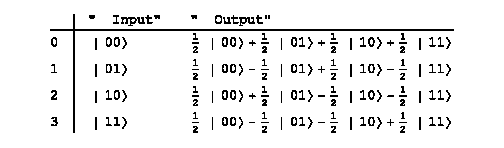

```mathematica
QuantumToGraphics[TraditionalForm[QuantumTableForm[Subscript[ℋ, OverHat[1]]⊗Subscript[ℋ, OverHat[2]]]]]
```

Using Grid[] and QuantumTable[] instead of QuantumTableForm[] a more beatiful table can be generated. This table can be copy-pasted to Microsoft Word because of the command QuantumToGraphics[]

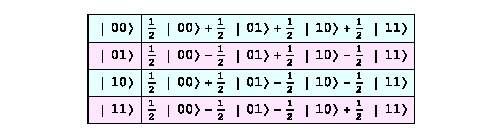

```mathematica
QuantumToGraphics[TraditionalForm[Grid[QuantumTable[Subscript[ℋ, OverHat[1]]⊗Subscript[ℋ, OverHat[2]]],Background->{None,{{LightCyan,LightMagenta}}},Frame->All]]]
```

Table headings can be added using Join[] and Style[] with the option ShowStringCharacters->False. This table can be copy-pasted to Microsoft Word because of the command QuantumToGraphics[]

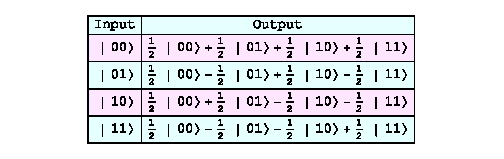

```mathematica
QuantumToGraphics[TraditionalForm[Style[Grid[Join[{{"Input","Output"}},QuantumTable[Subscript[ℋ, OverHat[1]]⊗Subscript[ℋ, OverHat[2]]]],Background->{None,{{LightCyan,LightMagenta}}},Frame->All],ShowStringCharacters->False]]]
```

Same example, with differente color for the headings:

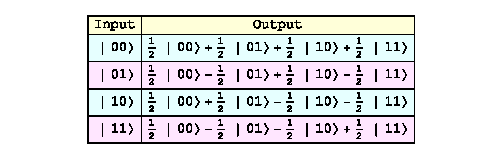

```mathematica
QuantumToGraphics[TraditionalForm[Style[Grid[Join[{{"Input","Output"}},QuantumTable[Subscript[ℋ, OverHat[1]]⊗Subscript[ℋ, OverHat[2]]]],Background->{None,{{LightYellow,LightCyan,LightMagenta,LightCyan,LightMagenta}}},Frame->All],ShowStringCharacters->False]]]
```

Another option is to Export[] as a figure. Here we export to a PDF graphic that can be read with Acrobat reader:

```mathematica
Export["myfig01.PDF",TraditionalForm[Style[Grid[Join[{{"Input","Output"}},QuantumTable[Subscript[ℋ, OverHat[1]]⊗Subscript[ℋ, OverHat[2]]]],Background->{None,{{LightYellow,LightCyan,LightMagenta,LightCyan,LightMagenta}}},Frame->All],ShowStringCharacters->False]]]
```

myfig01.PDF

Here we can see the file that was exported.

```mathematica
FileNames["myfig01.*"]
```

{myfig01.PDF}

Here we export to a GIF graphic that can be inserted in Microsoft Word documents and in HTML web pages:

```mathematica
Export["myfig02.GIF",TraditionalForm[Style[Grid[Join[{{"Input","Output"}},QuantumTable[Subscript[ℋ, OverHat[1]]⊗Subscript[ℋ, OverHat[2]]]],Background->{None,{{LightYellow,LightCyan,LightMagenta,LightCyan,LightMagenta}}},Frame->All],ShowStringCharacters->False]]]
```

myfig02.GIF

Here we can see the files that were exported.

```mathematica
FileNames["myf*.*"]
```

{myfig01.PDF,myfig02.GIF}

Style[] can be used to generate an expression in the desired format. This expression can be copy-pasted to Microsoft Word because of the command QuantumToGraphics[]

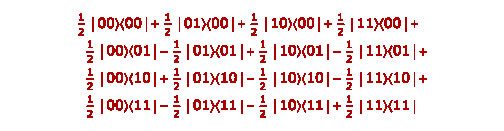

```mathematica
QuantumToGraphics[TraditionalForm[Style[QuantumEvaluate[Subscript[ℋ, OverHat[1]]⊗Subscript[ℋ, OverHat[2]]],Darker[Red],FontFamily->"Verdana"]]]
```

Notice the use of the option ItemSize in the QuantumToGraphics command. This expression can be copy-pasted to Microsoft Word because of the command QuantumToGraphics[]

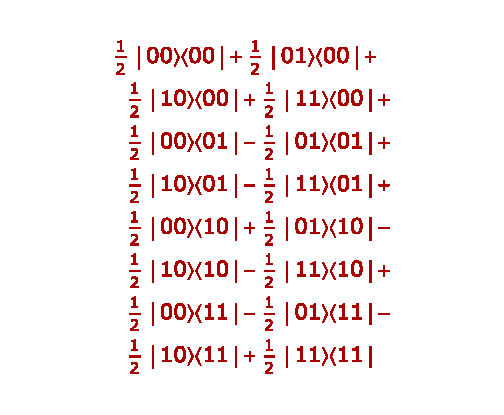

```mathematica
QuantumToGraphics[TraditionalForm[Style[QuantumEvaluate[Subscript[ℋ, OverHat[1]]⊗Subscript[ℋ, OverHat[2]]],Darker[Red],FontFamily->"Verdana"]],ItemSize->18]
```

Notice the use of the option ItemSize in the QuantumToGraphics command. This expression can be copy-pasted to Microsoft Word because of the command QuantumToGraphics[]

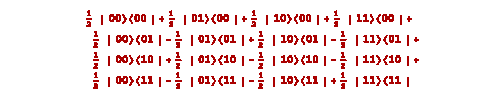

```mathematica
QuantumToGraphics[TraditionalForm[Style[QuantumEvaluate[Subscript[ℋ, OverHat[1]]⊗Subscript[ℋ, OverHat[2]]],Darker[Red],FontFamily->"Courier",FontWeight->"Bold"]],ItemSize->36]
```

by José Luis Gómez-Muñoz
http://homepage.cem.itesm.mx/lgomez/quantum/
jose.luis.gomez@itesm.mx